```mathematica
np=100; (* numero de primos*)
```

```mathematica
data=Table[{n,Prime[n]},{n,np}]; (* primeros np numeros primos*)
```

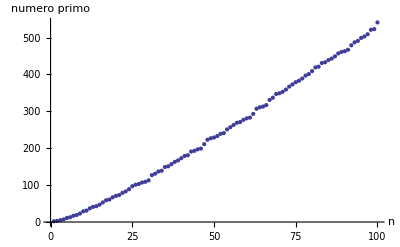

```mathematica
ListPlot[data, AxesLabel->{n,numero primo}]
```

-37.9697+5.53069 x

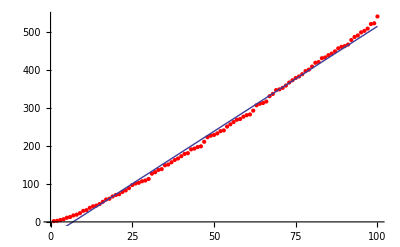

```mathematica
line=Fit[data,{1,x},x]
Show[ListPlot[data,PlotStyle->Red],Plot[{line},{x,0,np}]]
```

-14.9081+4.17412 x+0.0134313 x^2

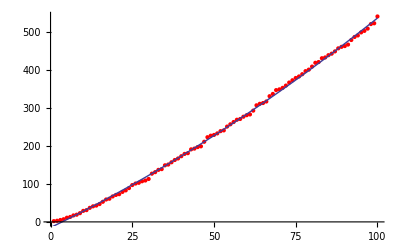

```mathematica
parabola=Fit[data,{1,x,x^2},x]
Show[ListPlot[data,PlotStyle->Red],Plot[{parabola},{x,0,np}]]
```

-6.34534+3.18138 x+0.0378823 x^2-0.000161393 x^3

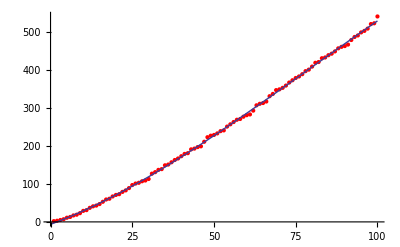

```mathematica
cubica=Fit[data,{1,x,x^2,x^3},x]
Show[ListPlot[data,PlotStyle->Red],Plot[{cubica},{x,0,np}]]
```

-4.11294+2.75824 x+0.0565169 x^2-0.000447434 x^3+1.41604×10^-6 x^4

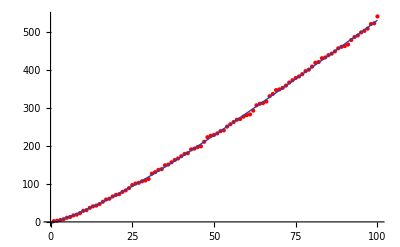

```mathematica
cuartica=Fit[data,{1,x,x^2,x^3,x^4},x]
Show[ListPlot[data,PlotStyle->Red],Plot[{cuartica},{x,0,np}]]
```

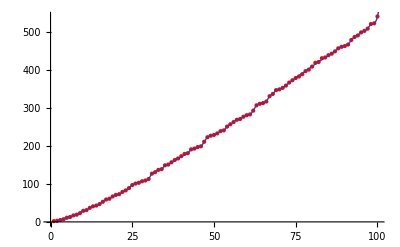

```mathematica
f=Interpolation[data];
Show[ListPlot[data,PlotStyle->Red],Plot[f[x],{x,1,200}]]
```

```mathematica
PrimeQ[f[111]]
```

InterpolatingFunction::dmval: Input value {111} lies outside the range of data in the interpolating function. Extrapolation will be used.

False

```mathematica
f[2]
```

3

```mathematica
For[i=100,i≤110,i++,
Print[i," ",f[i],"  ",PrimeQ[f[i]]]
]
```

100 541  True

InterpolatingFunction::dmval: Input value {101} lies outside the range of data in the interpolating function. Extrapolation will be used.

101 601  True

InterpolatingFunction::dmval: Input value {102} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

102 729  False

103 951  False

104 1293  False

105 1781  False

106 2441  True

107 3299  True

108 4381  False

109 5713  False

110 7321  True

```mathematica
For[n=1,n≤20,n++,
Print["n= ",n," ",2 n^2+29,"  ", PrimeQ[2 n^2+29]]
]
```

n= 1 31  True

n= 2 37  True

n= 3 47  True

n= 4 61  True

n= 5 79  True

n= 6 101  True

n= 7 127  True

n= 8 157  True

n= 9 191  True

n= 10 229  True

n= 11 271  True

n= 12 317  True

n= 13 367  True

n= 14 421  True

n= 15 479  True

n= 16 541  True

n= 17 607  True

n= 18 677  True

n= 19 751  True

n= 20 829  True